{0.080544,-0.94141,0.300789,1.39375,-0.88757,0.943421}

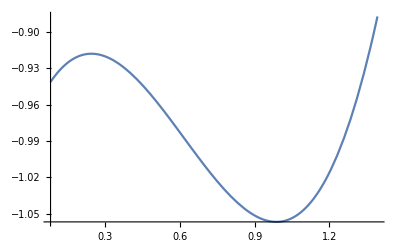

{-1.05654,{x→0.987711}}

```mathematica
Clear[f]
coeff=RandomReal[{-2,2},4];
a=RandomReal[{-2,2}];
b=RandomReal[{-2,2}];
f[x_]=Sum[coeff[[i+1]] x^i,{i,0,3}];
{a,f[a],D[f[x],x]/.x->a,b,f[b],D[f[x],{x,1}]/.x->b}
Plot[f[x],{x,Min[a,b],Max[a,b]}]
Minimize[{f[x],Min[a,b]≤x≤Max[a,b]},x]
```

71.4246

{45.9449-46.1541 x+238.183 x^2-119.596 x^3}

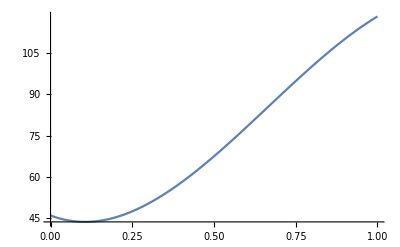

{43.5862,{x→0.105228}}

```mathematica
p=Sum[{p1,p2,p3,p4}[[i+1]] x^i,{i,0,3}];
a=0.0;pa=45.9449;dpa=-46.1541;b=1.0;pb=118.378;dpb=71.4246
ps=p/.Solve[{(p/.x->a)==pa,(D[p,x]/.x->a)==dpa,(p/.x->b)==pb,(D[p,x]/.x->b)==dpb
},
{p1,p2,p3,p4}]
Plot[ps[[1]],{x,a,b}]
Minimize[ps,x]
```